#### Magnetic scalar potential

Let B=μ H+Δ B inside the material (paramagnetic + offset).

Adapting Jackson eqn 5.120, we have to solve the system:

```mathematica
eqns={
α1-b^3 β1-γ1==b^3 H0,
2α1+μ b^3 β1-2μ γ1==-b^3 H0+b^3 ΔB,
a^3 β1+γ1-a^3 δ1==0,
μ a^3 β1-2μ γ1-a^3 δ1-a^3 ΔB==0
};
```

The solution is:

```mathematica
soln=Solve[eqns,{α1,β1,γ1,δ1}]//FullSimplify
```

{{α1→(b^3 (-a^3+b^3) (ΔB+H0 (-1+μ)) (1+2 μ))/(-2 a^3 (-1+μ)^2+b^3 (2+μ) (1+2 μ)),β1→(2 a^3 ΔB (-1+μ)+b^3 (3 H0-ΔB) (1+2 μ))/(2 a^3 (-1+μ)^2-b^3 (2+μ) (1+2 μ)),γ1→(3 a^3 b^3 (ΔB+H0 (-1+μ)))/(2 a^3 (-1+μ)^2-b^3 (2+μ) (1+2 μ)),δ1→(2 a^3 ΔB (-1+μ)+b^3 (-2 ΔB (-1+μ)+9 H0 μ))/(2 a^3 (-1+μ)^2-b^3 (2+μ) (1+2 μ))}}

```mathematica
Collect[(δ1/.soln),ΔB]
```

{(ΔB (2 a^3 (-1+μ)-2 b^3 (-1+μ)))/(2 a^3 (-1+μ)^2-b^3 (2+μ) (1+2 μ))+(9 b^3 H0 μ)/(2 a^3 (-1+μ)^2-b^3 (2+μ) (1+2 μ))}

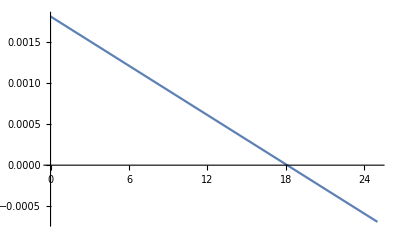

```mathematica
sub={μ0->1,a->1,b->1.1,μ->10000,H0->1};
Plot[
(-δ1/.soln)/.sub,
{ΔB,0,25}
]
```

#### Field

```mathematica
Φin[r_,θ_]:=δ1 r Cos[θ];
Φmid[r_,θ_]:=(β1+γ1/r^3) r Cos[θ];
Φout[r_,θ_]:=(-H0+α1/r^3) r Cos[θ];
```

The field is the negative gradient of the field:

```mathematica
Hin=Grad[Φin[r,θ],{r,θ,ϕ},"Spherical"]//FullSimplify
```

{δ1 Cos[θ],-δ1 Sin[θ],0}

```mathematica
Hmid=Grad[Φmid[r,θ],{r,θ,ϕ},"Spherical"]//FullSimplify
```

{(β1-(2 γ1)/r^3) Cos[θ],-(β1+γ1/r^3) Sin[θ],0}

```mathematica
Hout=Grad[Φout[r,θ],{r,θ,ϕ},"Spherical"]//FullSimplify
```

{(-H0-(2 α1)/r^3) Cos[θ],(H0-α1/r^3) Sin[θ],0}

Express it in Cartesian coordinates:

```mathematica
rhat={Sin[θ]Cos[ϕ], Sin[θ]Sin[ϕ], Cos[θ]};
θhat={Cos[θ]Cos[ϕ], Cos[θ]Sin[ϕ],-Sin[θ]};
ϕhat={-Sin[ϕ], Cos[ϕ],0};
```

```mathematica
HinC=Flatten[Hin.{rhat,θhat,ϕhat}]//FullSimplify
```

{0,0,δ1}

```mathematica
HmidC=Flatten[Hmid.{rhat,θhat,ϕhat}]//FullSimplify
```

{-(3 γ1 Cos[θ] Cos[ϕ] Sin[θ])/r^3,-(3 γ1 Cos[θ] Sin[θ] Sin[ϕ])/r^3,β1-γ1/(2 r^3)-(3 γ1 Cos[2 θ])/(2 r^3)}

```mathematica
HoutC=Flatten[Hout.{rhat,θhat,ϕhat}]//FullSimplify
```

{-(3 α1 Cos[θ] Cos[ϕ] Sin[θ])/r^3,-(3 α1 Cos[θ] Sin[θ] Sin[ϕ])/r^3,-(2 H0 r^3+α1+3 α1 Cos[2 θ])/(2 r^3)}

#### Energy density

```mathematica
uin3=(HinC.( HinC))/.soln[[1]]//FullSimplify
```

((2 a^3 ΔB (-1+μ)+b^3 (-2 ΔB (-1+μ)+9 H0 μ))^2)/((-2 a^3 (-1+μ)^2+b^3 (2+μ) (1+2 μ))^2)

```mathematica
umid3=Collect[(HmidC.( μ HmidC+ΔB))/.soln[[1]],r,FullSimplify]
```

((2 a^3 ΔB (-1+μ)+b^3 (3 H0-ΔB) (1+2 μ)) (2 a^3 ΔB (-1+μ) (-1+2 μ)+b^3 (1+2 μ) (3 H0 μ-2 ΔB (1+μ))))/(-2 a^3 (-1+μ)^2+b^3 (2+μ) (1+2 μ))^2+(9 a^6 b^6 (ΔB+H0 (-1+μ))^2 μ (5+3 Cos[2 θ]))/(2 r^6 (-2 a^3 (-1+μ)^2+b^3 (2+μ) (1+2 μ))^2)+(3 a^3 b^3 (ΔB+H0 (-1+μ)) (-(2 a^3 ΔB (-1+μ) (-1+3 μ)+b^3 (1+2 μ) (6 H0 μ-ΔB (2+3 μ))) (1+3 Cos[2 θ])+3 ΔB (-2 a^3 (-1+μ)^2+b^3 (2+μ) (1+2 μ)) Cos[ϕ] Sin[2 θ]+3 ΔB (-2 a^3 (-1+μ)^2+b^3 (2+μ) (1+2 μ)) Sin[2 θ] Sin[ϕ]))/(2 r^3 (-2 a^3 (-1+μ)^2+b^3 (2+μ) (1+2 μ))^2)

```mathematica
uout3=Collect[((HoutC.( HoutC)-H0^2)/.soln[[1]]),r,FullSimplify]
```

(b^3 (-a^3+b^3) H0 (ΔB+H0 (-1+μ)) (1+2 μ) (1+3 Cos[2 θ]))/(r^3 (-2 a^3 (-1+μ)^2+b^3 (2+μ) (1+2 μ)))+(b^6 (a^3-b^3)^2 (ΔB+H0 (-1+μ))^2 (1+2 μ)^2 (5+3 Cos[2 θ]))/(2 r^6 (-2 a^3 (-1+μ)^2+b^3 (2+μ) (1+2 μ))^2)

#### Integrated energy

```mathematica
$Assumptions:={a>0,b>0,a<b,H0>0,μ≥0,μ0>0,Im[ΔB]==0}
```

```mathematica
Uin3=2π∫_0^a r^2(∫_0^π uin3 Sin[θ]ⅆθ)ⅆr
```

(4 a^3 π (2 a^3 ΔB (-1+μ)+b^3 (-2 ΔB (-1+μ)+9 H0 μ))^2)/(3 (-2 a^3 (-1+μ)^2+b^3 (2+μ) (1+2 μ))^2)

```mathematica
Umid3=2π∫_a^b r^2(∫_0^π umid3 Sin[θ]ⅆθ)ⅆr
```

-((4 (a^3-b^3) π (4 a^6 ΔB^2 (-1+μ)^2 (-1+2 μ)+b^6 (3 H0-ΔB) (1+2 μ)^2 (3 H0 μ-2 ΔB (1+μ))+2 a^3 b^3 (9 H0^2 (-1+μ)^2 μ+ΔB^2 (1+2 μ (7+μ-4 μ^2))+3 H0 ΔB (1+μ (-8+μ+6 μ^2)))))/(3 (-2 a^3 (-1+μ)^2+b^3 (2+μ) (1+2 μ))^2))

```mathematica
Uout3=2π∫_b^∞ r^2(∫_0^π uout3 Sin[θ]ⅆθ)ⅆr
```

(8 b^3 (a^3-b^3)^2 π (ΔB+H0 (-1+μ))^2 (1+2 μ)^2)/(3 (-2 a^3 (-1+μ)^2+b^3 (2+μ) (1+2 μ))^2)

```mathematica
Utotal3=Uin3+Umid3+Uout3//FullSimplify
```

(4 π (-4 a^6 ΔB^2 (-1+μ)-b^6 (1+2 μ) (-5 H0 ΔB+2 ΔB^2+H0^2 (1+2 μ))+a^3 b^3 (2 ΔB^2 (-1+4 μ)+H0^2 (-1+μ) (-1+4 μ)-5 H0 (ΔB+2 ΔB μ))))/(6 a^3 (-1+μ)^2-3 b^3 (2+μ) (1+2 μ))

```mathematica
minU3=Solve[D[Utotal3,ΔB]==0,ΔB][[1,1]]//FullSimplify
```

ΔB→-(5 b^3 H0 (1+2 μ))/(8 a^3 (-1+μ)-4 b^3 (1+2 μ))

```mathematica
Bin3min=-(2 a^3 ΔB (-1+μ)+b^3 (-2 ΔB (-1+μ)+9 H0 μ))/(2 a^3 (-1+μ)^2-b^3 (2+μ) (1+2 μ))/.minU3//FullSimplify
```

1/4 b^3 H0 (5/(-2 a^3 (-1+μ)+b^3 (1+2 μ))-(21 μ)/(2 a^3 (-1+μ)^2-b^3 (2+μ) (1+2 μ)))

```mathematica
Series[Bin3min,{μ,∞,1}]
```

-(13 (b^3 H0))/(4 (a^3-b^3) μ)+O[1/μ]^2

```mathematica
-(13 (b^3 H0))/(4 (a^3-b^3) μ)/.{b->1.1*a}
```

(13.0687 H0)/μ

```mathematica
13./4
```

3.25

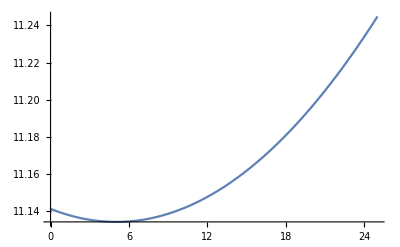

```mathematica
Plot[Utotal3/.sub,{ΔB,0,25}]
```